Henry Osei

```mathematica
f[x_]:=x^2Sin[x]
dq=f'[x]
edq=Expand[dq]
Limit[edq,h->0]
```

x^2 Cos[x]+2 x Sin[x]

x^2 Cos[x]+2 x Sin[x]

x (x Cos[x]+2 Sin[x])

```mathematica
f[x_]:=1/1-4/x
dq=(f[x+h]-f[x])/h
edq=Expand[dq]
Limit[edq,h->0]
```

(4/x-4/(h+x))/h

4/(h x)-4/(h (h+x))

4/x^2

```mathematica
f[x_]:=x/Sqrt[1+x^2]
dq=(f[x+h]-f[x])/h
edq=Expand[dq]
Limit[edq,h->0]
```

(-x/(√(1+x^2))+(h+x)/(√(1+(h+x)^2)))/h

-x/(h √(1+x^2))+1/(√(1+(h+x)^2))+x/(h √(1+(h+x)^2))

1/((1+x^2)^(3/2))

```mathematica
f[x_]:=x Sin[x^2]
dq=f'[x]
edq=Expand[dq]
Limit[edq,h->0]
```

2 x^2 Cos[x^2]+Sin[x^2]

2 x^2 Cos[x^2]+Sin[x^2]

2 x^2 Cos[x^2]+Sin[x^2]

```mathematica
f[x_]:=x+Sqrt[x]
dq=f'[x]//Simplify
edq=Expand[dq]
Limit[edq,h->0]
```

1+1/(2 √x)

1+1/(2 √x)

1+1/(2 √x)

```mathematica
f[x_]:=1/x^2
dq=(f[x+h]-f[x])/h
edq=Expand[dq]
Limit[edq,h->0]
```

(-1/x^2+1/(h+x)^2)/h

-1/(h x^2)+1/(h (h+x)^2)

-2/x^3

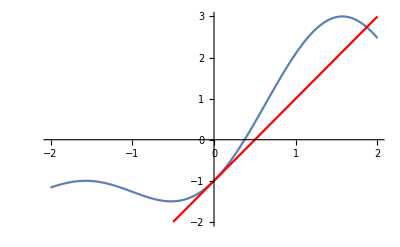

```mathematica
Clear[f,x]
f[x_]:=2  Sin[x]-(Cos[2x])
f1[x_]:=f'[0](x-0)+f[0]
Plot[{f[x],f1[x]},{x,-2,2},PlotRange->{-2,3},PlotStyle->{{},RGBColor[1,0,0]}]
```

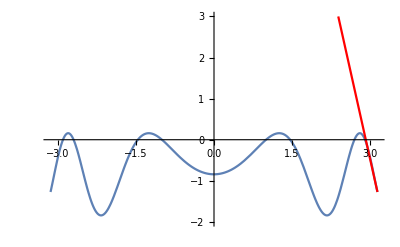

```mathematica
Clear[f,x]
f[x_]:=Sin[x^2]-Sin [x/x]
f1[x_]:=f'[Pi](x-Pi)+f[Pi]
Plot[{f[x],f1[x]},{x,-Pi,Pi},PlotRange->{-2,3},PlotStyle->{{},RGBColor[1,0,0]}]
```

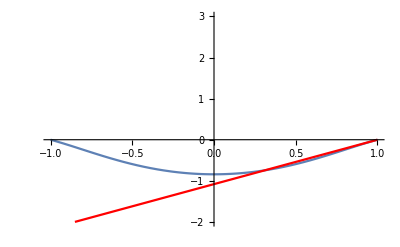

```mathematica
Clear[f,x]
f[x_]:=Sin[x^2]-Sin [x/x]
f1[x_]:=f'[1](x-1)+f[1]
Plot[{f[x],f1[x]},{x,-1,1},PlotRange->{-2,3},PlotStyle->{{},RGBColor[1,0,0]}]
```

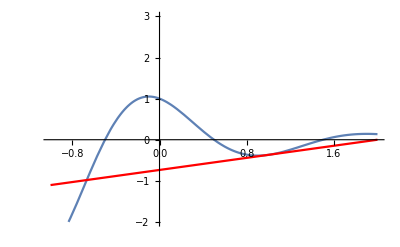

```mathematica
Clear[f,x]
f[x_]:=Exp[-x]Cos [Pi(x)]
f1[x_]:=f'[1](x-1)+f[1]
Plot[{f[x],f1[x]},{x,-1,2},PlotRange->{-2,3},PlotStyle->{{},RGBColor[1,0,0]}]
```

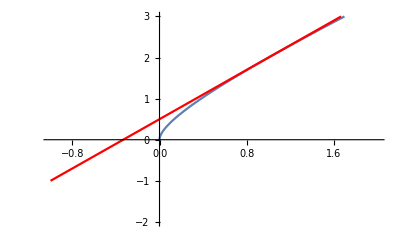

```mathematica
Clear[f,x]
f[x_]:=x+Sqrt[x]
f1[x_]:=f'[1](x-1)+f[1]
Plot[{f[x],f1[x]},{x,-1,2},PlotRange->{-2,3},PlotStyle->{{},RGBColor[1,0,0]}]
```

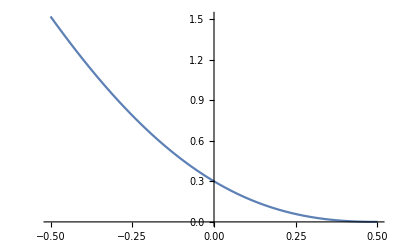

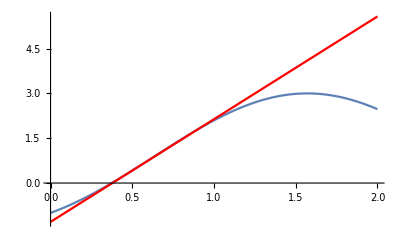

```mathematica
Clear [f,x]
f[x_]:=2Sin [x]-Cos [2x]
f1[x_]:=f'[0.5](x-0.5)+f[0.5]
Plot[Abs[f[x]-f1[x]],{x,-.5,.5}]
Plot[{f[x],f1[x]},{x,0,2},PlotStyle->{{},RGBColor[1,0,0]}]
```

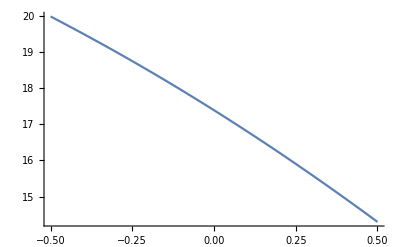

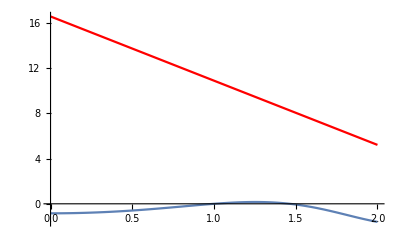

```mathematica
Clear [f,x]
f[x_]:=Sin [x^2]-Sin [x/x]
f1[x_]:=f'[Pi](x-Pi)+f[Pi]
Plot[Abs[f[x]-f1[x]],{x,-.5,.5}]
Plot[{f[x],f1[x]},{x,0,2},PlotStyle->{{},RGBColor[1,0,0]}]
```

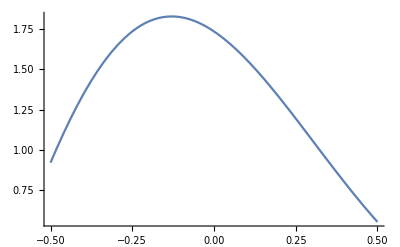

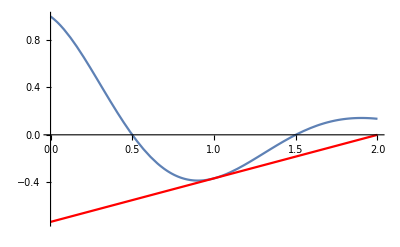

```mathematica
Clear [f,x]
f[x_]:=Exp[-x]Cos [Pi (x)]
f1[x_]:=f'[1](x-1)+f[1]
Plot[Abs[f[x]-f1[x]],{x,-.5,.5}]
Plot[{f[x],f1[x]},{x,0,2},PlotStyle->{{},RGBColor[1,0,0]}]
```

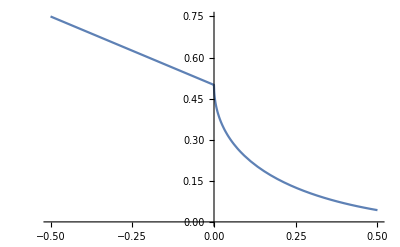

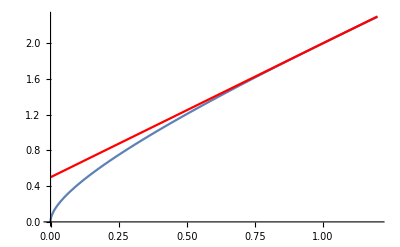

```mathematica
Clear [f,x]
f[x_]:=x+Sqrt[x]
f1[x_]:=f'[1](x-1)+f[1]
Plot[Abs[f[x]-f1[x]],{x,-.5,.5}]
Plot[{f[x],f1[x]},{x,0,1.2},PlotStyle->{{},RGBColor[1,0,0]}]
```

```mathematica
Clear [f,x]
f2[x_]:=a x^2+b x+c
0f2[0]
```

0

```mathematica
f2[0]
```

c

```mathematica
f2'[0]
```

b

```mathematica
f2''[0]
```

2 a

```mathematica
Clear [f,x]
f2[x_]:=a x^2+b x+c
0f2[0]
```

0

```mathematica
f2'[0]
```

b

```mathematica
f2''[0]
```

2 a

```mathematica
Clear [f,x]
f3[x_]:=a (x-Pi)^3+b (x-Pi)^2+c(x-Pi)+d
0f3[0]
```

0

```mathematica
f3[0]
```

d-c π+b π^2-a π^3

```mathematica
f3'[0]
```

c-2 b π+3 a π^2

```mathematica
f3''[0]
```

2 b-6 a π

SetDelayed::write: Tag Times in _\ f[x] is Protected.

SetDelayed::write: Tag Times in (c + b\ x + a\ x^2)\ _ is Protected.